```mathematica
(* Mathematica*)
```

```mathematica
(*Hyperbolic Discriminate prime manifolds found in Reid-Maclachlan:{3,7,11,23,32,...59,,,,107}*)
```

```mathematica
(* square free primes:A039787*)
```

```mathematica
(*https://oeis.org/A039787*)
```

```mathematica
w=Select[Prime[Range[200]],SquareFreeQ[#-1]&];
```

```mathematica
Union[Table[(w[[i+1]]-w[[i]])/4,{i,2,Length[w]-1}]]
```

{1,2,3,4,5,6,7,9,10,11,12}

```mathematica
max=Max[Table[(w[[i+1]]-w[[i]])/4,{i,2,Length[w]-1}]]
```

12

```mathematica
sq=Flatten[Union[Table[If[(w[[i+1]]-w[[i]])/4==max,{i+1,w[[i+1]]},{}],{i,2,Length[w]-1}]]][[1]]
```

72

```mathematica
(*Find 11 primes for test search*)
```

```mathematica
Table[w[[i]],{i,sq-11,sq-1}]
```

{863,887,907,911,947,967,971,983,1019,1031,1039}

```mathematica
(*test searcrches*)
```

```mathematica
(*You submitted the polynomial sequence of order 9:7583 7591 7603 7607 7639 7643 7691 7699 7703 7727
Corresponding to the equation:-11/1008x9+2221/5040x8-18821/2520x7+24839/360x6-54341/144x5+892867/720x4-248086/105x3+986357/420x2-6317/7x+7583
11 primes for category 1:7583 7591 7603 7607 7639 7643 7691 7699 7703 7727 283
12 primes for category 2:7583 7591 7603 7607 7639 7643 7691 7699 7703 7727 283 61409
35 primes for category 3 in the range from x=0 to 120
Score for category 1:11+1/log(10+absolute(7583*7591*7603*7607*7639*7643*7691*7699*7703*7727))=11.025749485932
Score for category 2:12+1/log(10+absolute(7583*7591*7603*7607*7639*7643*7691*7699*7703*7727))=12.025749485932
Score for category 3:35+1/log(10+absolute(7583*7591*7603*7607*7639*7643*7691*7699*7703*7727))=35.025749485932
Elapsed time:0.031243085861206 seconds&)*)
```

```mathematica
(*You submitted the polynomial sequence of order 10:6199 6203 6263 6271 6287 6299 6311 6323 6343 6367 6379
Corresponding to the equation:11/36288x10-191/12096x9+10747/30240x8-15203/3360x7+309331/8640x6-104755/576x5+13381201/22680x4-17690009/15120x3+1600001/1260x2-11248/21x+6199
11 primes for category 1:6199 6203 6263 6271 6287 6299 6311 6323 6343 6367 6379
11 primes for category 2:6199 6203 6263 6271 6287 6299 6311 6323 6343 6367 6379
20 primes for category 3 in the range from x=0 to 60
Score for category 1:11+1/log(10+absolute(6199*6203*6263*6271*6287*6299*6311*6323*6343*6367*6379))=11.023929879008
Score for category 2:11+1/log(10+absolute(6199*6203*6263*6271*6287*6299*6311*6323*6343*6367*6379))=11.023929879008
Score for category 3:20+1/log(10+absolute(6199*6203*6263*6271*6287*6299*6311*6323*6343*6367*6379))=20.023929879008
Elapsed time:0.083343029022217 seconds*)
```

```mathematica
(*You submitted the polynomial sequence of order 10:2 3 7 11 23 31 43 47 59 67 71
Corresponding to the equation:53/134400x10-14237/725760x9+4217/10080x8-604763/120960x7+2114741/57600x6-1179877/6912x5+20090507/40320x4-157944733/181440x3+4558907/5600x2-761731/2520x+2
11 primes for category 1:2 3 7 11 23 31 43 47 59 67 71
11 primes for category 2:2 3 7 11 23 31 43 47 59 67 71
14 primes for category 3 in the range from x=0 to 60
Score for category 1:11+1/log(10+absolute(2*3*7*11*23*31*43*47*59*67*71))=11.070069802925
Score for category 2:11+1/log(10+absolute(2*3*7*11*23*31*43*47*59*67*71))=11.070069802925
Score for category 3:14+1/log(10+absolute(2*3*7*11*23*31*43*47*59*67*71))=14.070069802925
Elapsed time:0.022218942642212 seconds*)
```

```mathematica
(* You submitted the polynomial sequence of order 10:3 7 11 23 31 43 47 59 67 71 79
Corresponding to the equation:-53/129600x10+743/36288x9-2657/6048x8+22807/4320x7-1683143/43200x6+1572439/8640x5-691975/1296x4+42581669/45360x3-1390201/1575x2+15028/45x+3
11 primes for category 1:3 7 11 23 31 43 47 59 67 71 79
11 primes for category 2:3 7 11 23 31 43 47 59 67 71 79
15 primes for category 3 in the range from x=0 to 60
Score for category 1:11+1/log(10+absolute(3*7*11*23*31*43*47*59*67*71*79))=11.063019596266
Score for category 2:11+1/log(10+absolute(3*7*11*23*31*43*47*59*67*71*79))=11.063019596266
Score for category 3:15+1/log(10+absolute(3*7*11*23*31*43*47*59*67*71*79))=15.063019596266
Elapsed time:0.032029867172241 seconds*)
```

```mathematica
(* You submitted the polynomial sequence of order 10:7 11 23 31 43 47 59 67 71 79 83
Corresponding to the equation:103/302400x10-1049/60480x9+3817/10080x8-9335/2016x7+500459/14400x6-158311/960x5+7417597/15120x4-2641211/3024x3+1313999/1575x2-10956/35x+7
11 primes for category 1:7 11 23 31 43 47 59 67 71 79 83
11 primes for category 2:7 11 23 31 43 47 59 67 71 79 83
19 primes for category 3 in the range from x=0 to 60
Score for category 1:11+1/log(10+absolute(7*11*23*31*43*47*59*67*71*79*83))=11.057769951901
Score for category 2:11+1/log(10+absolute(7*11*23*31*43*47*59*67*71*79*83))=11.057769951901
Score for category 3:19+1/log(10+absolute(7*11*23*31*43*47*59*67*71*79*83))=19.057769951901
Elapsed time:0.0068161487579346 seconds*)
```

```mathematica
(* You submitted the polynomial sequence of order 10:11 23 31 43 47 59 67 71 79 83 103
Corresponding to the equation:-151/907200x10+179/20160x9-439/2160x8+26279/10080x7-886663/43200x6+293893/2880x5-28781957/90720x4+2959823/5040x3-1040419/1800x2+3305/14x+11
11 primes for category 1:11 23 31 43 47 59 67 71 79 83 103
11 primes for category 2:11 23 31 43 47 59 67 71 79 83 103
18 primes for category 3 in the range from x=0 to 60
Score for category 1:11+1/log(10+absolute(11*23*31*43*47*59*67*71*79*83*103))=11.05411906685
Score for category 2:11+1/log(10+absolute(11*23*31*43*47*59*67*71*79*83*103))=11.05411906685
Score for category 3:18+1/log(10+absolute(11*23*31*43*47*59*67*71*79*83*103))=18.05411906685
Elapsed time:0.022680044174194 seconds*)
```

```mathematica
(*You submitted the polynomial sequence of order 10:23 31 43 47 59 67 71 79 83 103 107
Corresponding to the equation:-61/907200x10+499/181440x9-673/15120x8+1483/4320x7-42253/43200x6-29177/8640x5+3174973/90720x4-4878829/45360x3+1814717/12600x2-5347/90x+23
11 primes for category 1:23 31 43 47 59 67 71 79 83 103 107
11 primes for category 2:23 31 43 47 59 67 71 79 83 103 107
13 primes for category 3 in the range from x=0 to 60
Score for category 1:11+1/log(10+absolute(23*31*43*47*59*67*71*79*83*103*107))=11.051372236712
Score for category 2:11+1/log(10+absolute(23*31*43*47*59*67*71*79*83*103*107))=11.051372236712
Score for category 3:13+1/log(10+absolute(23*31*43*47*59*67*71*79*83*103*107))=13.051372236712
Elapsed time:0.0038070678710938 seconds*)
```

```mathematica
(* You submitted the polynomial sequence of order 10:587 599 607 619 643 647 659 683 691 719 743
Corresponding to the equation:29/151200x10-47/4320x9+661/2520x8-5897/1680x7+205517/7200x6-208837/1440x5+6883459/15120x4-906373/1080x3+5102611/6300x2-30893/105x+587
11 primes for category 1:587 599 607 619 643 647 659 683 691 719 743
11 primes for category 2:587 599 607 619 643 647 659 683 691 719 743
25 primes for category 3 in the range from x=0 to 60
Score for category 1:11+1/log(10+absolute(587*599*607*619*643*647*659*683*691*719*743))=11.032299155932
Score for category 2:11+1/log(10+absolute(587*599*607*619*643*647*659*683*691*719*743))=11.032299155932
Score for category 3:25+1/log(10+absolute(587*599*607*619*643*647*659*683*691*719*743))=25.032299155932
Elapsed time:0.053745031356812 seconds*)
```

```mathematica
(*You submitted the polynomial sequence of order 10:983 1019 1031 1039 1087 1091 1103 1123 1163 1187 1223
Corresponding to the equation:367/302400x10-107/1728x9+1711/1260x8-8027/480x7+1824311/14400x6-1749341/2880x5+55135751/30240x4-7031171/2160x3+38690573/12600x2-33199/30x+983
11 primes for category 1:983 1019 1031 1039 1087 1091 1103 1123 1163 1187 1223
11 primes for category 2:983 1019 1031 1039 1087 1091 1103 1123 1163 1187 1223
21 primes for category 3 in the range from x=0 to 60
Score for category 1:11+1/log(10+absolute(983*1019*1031*1039*1087*1091*1103*1123*1163*1187*1223))=11.029917665058
Score for category 2:11+1/log(10+absolute(983*1019*1031*1039*1087*1091*1103*1123*1163*1187*1223))=11.029917665058
Score for category 3:21+1/log(10+absolute(983*1019*1031*1039*1087*1091*1103*1123*1163*1187*1223))=21.029917665058
Elapsed time:0.029112815856934 seconds*)
```

```mathematica
(*You submitted the polynomial sequence of order 10:1811 1823 1831 1847 1867 1871 1879 1907 1931 1979 1987
Corresponding to the equation:-61/907200x10+47/20160x9-163/6048x8+47/1120x7+74807/43200x6-5407/320x5+644839/9072x4-760679/5040x3+80438/525x2-4853/105x+1811
11 primes for category 1:1811 1823 1831 1847 1867 1871 1879 1907 1931 1979 1987
11 primes for category 2:1811 1823 1831 1847 1867 1871 1879 1907 1931 1979 1987
19 primes for category 3 in the range from x=0 to 60
Score for category 1:11+1/log(10+absolute(1811*1823*1831*1847*1867*1871*1879*1907*1931*1979*1987))=11.027757898594
Score for category 2:11+1/log(10+absolute(1811*1823*1831*1847*1867*1871*1879*1907*1931*1979*1987))=11.027757898594
Score for category 3:19+1/log(10+absolute(1811*1823*1831*1847*1867*1871*1879*1907*1931*1979*1987))=19.027757898594
Elapsed time:0.031080961227417 seconds*)
```

```mathematica
(*You submitted the polynomial sequence of order 10:3371 3391 3407 3463 3467 3491 3499 3527 3539 3559 3571
Corresponding to the equation:-283/181440x10+14323/181440x9-51913/30240x8+634177/30240x7-272723/1728x6+6514807/8640x5-102847193/45360x4+185374817/45360x3-1238297/315x2+95519/63x+3371
11 primes for category 1:3371 3391 3407 3463 3467 3491 3499 3527 3539 3559 3571
11 primes for category 2:3371 3391 3407 3463 3467 3491 3499 3527 3539 3559 3571
18 primes for category 3 in the range from x=0 to 60
Score for category 1:11+1/log(10+absolute(3371*3391*3407*3463*3467*3491*3499*3527*3539*3559*3571))=11.025669220541
Score for category 2:11+1/log(10+absolute(3371*3391*3407*3463*3467*3491*3499*3527*3539*3559*3571))=11.025669220541
Score for category 3:18+1/log(10+absolute(3371*3391*3407*3463*3467*3491*3499*3527*3539*3559*3571))=18.025669220541
Elapsed time:0.0092999935150146 seconds*)
```

```mathematica
(*You submitted the polynomial sequence of order 10:7639 7643 7691 7699 7703 7727 7823 7879 7883 7907 7919
Corresponding to the equation:299/226800x10-6011/90720x9+43051/30240x8-258287/15120x7+338873/2700x6-2516423/4320x5+154143757/90720x4-33873821/11340x3+35884183/12600x2-682439/630x+7639
12 primes for category 1:7639 7643 7691 7699 7703 7727 7823 7879 7883 7907 7919 15427
12 primes for category 2:7639 7643 7691 7699 7703 7727 7823 7879 7883 7907 7919 15427
14 primes for category 3 in the range from x=0 to 60
Score for category 1:12+1/log(10+absolute(7639*7643*7691*7699*7703*7727*7823*7879*7883*7907*7919))=12.023366338719
Score for category 2:12+1/log(10+absolute(7639*7643*7691*7699*7703*7727*7823*7879*7883*7907*7919))=12.023366338719
Score for category 3:14+1/log(10+absolute(7639*7643*7691*7699*7703*7727*7823*7879*7883*7907*7919))=14.023366338719
Elapsed time:0.012237071990967 seconds*)
```

```mathematica
(* end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear[a,p,q,x]
```

```mathematica
(* test rational decic polynomial*)
```

```mathematica
p[x_]=-59/302400x^10+607/60480x^9-443/2016x^8+26917/10080x^7-283687/14400x^6+261379/2880x^5-195829/756x^4+6647057/15120x^3-2551793/6300x^2+6123/35x+1787
```

1787+(6123 x)/35-(2551793 x^2)/6300+(6647057 x^3)/15120-(195829 x^4)/756+(261379 x^5)/2880-(283687 x^6)/14400+(26917 x^7)/10080-(443 x^8)/2016+(607 x^9)/60480-(59 x^10)/302400

```mathematica
x/.NSolve[p[x]==0,x]
```

{-1.09043,0.0843292-2.19884 ⅈ,0.0843292+2.19884 ⅈ,3.13859-3.5133 ⅈ,3.13859+3.5133 ⅈ,7.07838-3.48214 ⅈ,7.07838+3.48214 ⅈ,10.2304-2.20617 ⅈ,10.2304+2.20617 ⅈ,11.4677}

```mathematica
Table[If[PrimeQ[p[x]],p[x],0],{x,0,99}]
```

{1787,1811,1823,1831,1847,1867,1871,1879,1907,1931,1979,1523,-5273,0,0,0,-2426933,0,0,0,0,-149862197,-285251401,0,0,0,0,0,0,0,0,0,-34768479461,-50440974733,0,0,0,0,0,-364679152793,0,0,-860057100853,0,0,0,0,-3102630088861,0,0,0,0,0,0,0,0,0,-26778292478501,0,0,0,0,0,0,0,0,-133568872666433,-157301900972473,0,0,0,0,0,0,0,0,0,0,0,0,-1065415587631093,0,0,0,0,0,-2307244279343657,0,0,-3323648048456773,0,0,0,0,0,0,-7419977171134117,0,0,0}

```mathematica
Table[If[PrimeQ[p[x-8]],p[x-8],0],{x,0,99}]
```

{-20293213,0,0,0,0,0,-12413,0,1787,1811,1823,1831,1847,1867,1871,1879,1907,1931,1979,1523,-5273,0,0,0,-2426933,0,0,0,0,-149862197,-285251401,0,0,0,0,0,0,0,0,0,-34768479461,-50440974733,0,0,0,0,0,-364679152793,0,0,-860057100853,0,0,0,0,-3102630088861,0,0,0,0,0,0,0,0,0,-26778292478501,0,0,0,0,0,0,0,0,-133568872666433,-157301900972473,0,0,0,0,0,0,0,0,0,0,0,0,-1065415587631093,0,0,0,0,0,-2307244279343657,0,0,-3323648048456773,0,0}

```mathematica
v=Table[p[x],{x,0,99}]
```

{1787,1811,1823,1831,1847,1867,1871,1879,1907,1931,1979,1523,-5273,-46885,-220853,-797677,-2426933,-6511933,-15846745,-35643505,-75119401,-149862197,-285251401,-521279873,-919198525,-1570495493,-2608821469,-4225585477,-6690070969,-10375061413,-15789118253,-23616822949,-34768479461,-50440974733,-72191713169,-102027777481,-142512723337,-196893689653,-269251800865,-364679152793,-489486010477,-651442205333,-860057100853,-1126902901565,-1465986509785,-1894175589541,-2431684977637,-3102630088861,-3935654496533,-4964639431645,-6229503534473,-7777101812449,-9662233407977,-11948768460469,-14710905058873,-18034568025073,-22018962045469,-26778292478501,-32443668010573,-39165200212469,-47114315963641,-56486299663397,-67503083136733,-80416302169045,-95510639668933,-113107476562477,-133568872666433,-157301900972473,-184763360000585,-216464890147765,-252978521268881,-294942680080777,-343068687379021,-398147776499893,-461058665948965,-532775720652653,-614377737871129,-707057395440677,-812131401691669,-931051388115533,-1065415587631093,-1216981343128189,-1387678492845241,-1579623681068113,-1795135644620969,-2036751527656501,-2307244279343657,-2609641191196513,-2947243632988925,-3323648048456773,-3742768274303677,-4208859248397733,-4726542175476793,-5300831221168805,-5937161807682445,-6641420587132421,-7419977171134117,-8279717698034381,-9228080321939953,-10273092710562985}

```mathematica
ListPlot[v]
```

-Graphics-

```mathematica
(* cubic plus gaps give {-1,2} generates primes*)
```

```mathematica
Sum[If[PrimeQ[Abs[p[x]]],1,0],{x,0,99}]
```

28

```mathematica
Sum[If[PrimeQ[Abs[p[x]-1]],1,0],{x,0,99}]
```

0

```mathematica
(* test for shift*)
```

```mathematica
(* negative shifts detect primes*)
```

```mathematica
Table[Max[Union[Table[Sum[If[PrimeQ[p[x]+Prime[n]+i],1,0],{x,0,99}],{n,100}]]],{i,-100,100}]
```

{4,14,8,28,13,26,2,26,26,23,13,28,5,23,23,26,6,28,4,20,20,28,8,25,5,17,14,28,12,28,3,15,15,28,13,25,3,17,12,28,9,28,3,17,10,25,9,28,6,17,12,26,12,28,7,17,11,28,13,28,2,17,17,28,17,21,3,14,10,28,9,28,3,21,21,25,8,28,5,15,10,28,4,28,4,15,13,28,12,28,6,18,18,28,9,28,4,28,28,21,8,26,2,15,10,20,11,26,3,15,15,25,6,26,3,15,11,25,9,22,8,17,17,26,9,26,5,14,10,27,10,26,4,15,15,26,8,26,5,14,12,26,9,25,7,16,11,27,8,27,3,15,14,26,10,21,2,16,14,22,12,27,4,17,17,26,8,27,8,15,10,27,12,26,8,16,10,25,8,27,5,15,15,27,13,26,1,17,17,22,4,27,5,15,14,25,6,26,5,17,17}

```mathematica
Union[Table[Max[Union[Table[Sum[If[PrimeQ[p[x]+Prime[n]+i],1,0],{x,0,99}],{n,100}]]],{i,-100,100}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,20,21,22,23,25,26,27,28}

```mathematica
maxs=Max[%]
```

28

```mathematica
Union[Table[If[Max[Union[Table[Sum[If[PrimeQ[Abs[p[x]+Prime[n]+i]],1,0],{x,0,99}],{n,100}]]]==maxs,{i,Max[Union[Table[Sum[If[PrimeQ[Abs[p[x]+Prime[n]+i]],1,0],{x,0,99}],{n,100}]]]},{}],{i,-100,100}]]
```

{{},{-97,28},{-89,28},{-83,28},{-79,28},{-73,28},{-71,28},{-67,28},{-61,28},{-59,28},{-53,28},{-47,28},{-43,28},{-41,28},{-37,28},{-31,28},{-29,28},{-23,28},{-19,28},{-17,28},{-13,28},{-11,28},{-7,28},{-5,28},{-3,28},{-2,28}}

```mathematica
(* experiment with 100 prime gaps finds higher Prime generater*)
```

```mathematica
wp=Table[Sum[If[PrimeQ[Abs[p[x]+Prime[n]-2]],1,0],{x,0,99}],{n,-100,100}]
```

Prime::intpp: Positive integer argument expected in Prime[-100].

General::stop: Further output of Prime::intpp will be suppressed during this calculation.

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,28,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
max=Max[wp]
```

28

```mathematica
q[x_]=Expand[Delete[Union[Table[If[Sum[If[PrimeQ[Abs[p[x]+Prime[n]-2]],1,0],{x,0,99}]==max,p[x]+Prime[n]-2,{}],{n,-100,100}]],2][[1]]/.x->x-0]
```

Prime::intpp: Positive integer argument expected in Prime[-100].

General::stop: Further output of Prime::intpp will be suppressed during this calculation.

1787+(6123 x)/35-(2551793 x^2)/6300+(6647057 x^3)/15120-(195829 x^4)/756+(261379 x^5)/2880-(283687 x^6)/14400+(26917 x^7)/10080-(443 x^8)/2016+(607 x^9)/60480-(59 x^10)/302400

```mathematica
Reverse[CoefficientList[q[x],x]]
```

{-59/302400,607/60480,-443/2016,26917/10080,-283687/14400,261379/2880,-195829/756,6647057/15120,-2551793/6300,6123/35,1787}

```mathematica
Sum[If[PrimeQ[q[x]],1,0],{x,0,99}]
```

28

```mathematica
Sum[If[PrimeQ[q[x]],1,0],{x,0,999}]
```

100

```mathematica
x/.NSolve[q[x]==0,x]
```

{-1.09043,0.0843292-2.19884 ⅈ,0.0843292+2.19884 ⅈ,3.13859-3.5133 ⅈ,3.13859+3.5133 ⅈ,7.07838-3.48214 ⅈ,7.07838+3.48214 ⅈ,10.2304-2.20617 ⅈ,10.2304+2.20617 ⅈ,11.4677}

```mathematica
Abs[%]
```

{1.09043,2.20046,2.20046,4.71105,4.71105,7.88852,7.88852,10.4656,10.4656,11.4677}

```mathematica
(* end*)
```

```mathematica
Table[If[PrimeQ[q[x]],q[x],0],{x,0,99}]
```

{1787,1811,1823,1831,1847,1867,1871,1879,1907,1931,1979,1523,-5273,0,0,0,-2426933,0,0,0,0,-149862197,-285251401,0,0,0,0,0,0,0,0,0,-34768479461,-50440974733,0,0,0,0,0,-364679152793,0,0,-860057100853,0,0,0,0,-3102630088861,0,0,0,0,0,0,0,0,0,-26778292478501,0,0,0,0,0,0,0,0,-133568872666433,-157301900972473,0,0,0,0,0,0,0,0,0,0,0,0,-1065415587631093,0,0,0,0,0,-2307244279343657,0,0,-3323648048456773,0,0,0,0,0,0,-7419977171134117,0,0,0}

```mathematica
wa=Table[If[PrimeQ[q[x]],1,0],{x,0,99}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0}

```mathematica
min=Min[Table[If[wa[[i]]==0,i,{}],{i,Length[wa]}]]
```

14

```mathematica
Sum[wa[[i]],{i,min}]
```

13

```mathematica
Table[If[PrimeQ[q[x]],q[x],{}],{x,0,min}]
```

{1787,1811,1823,1831,1847,1867,1871,1879,1907,1931,1979,1523,-5273,{},{}}

```mathematica
Length[Union[Table[If[PrimeQ[q[x]],q[x],{}],{x,0,min-2}]]]
```

13

```mathematica
ExpandAll[FindSequenceFunction[Table[q[x],{x,0,99}],x]]
```

395+(275279 x)/70-(57251611 x^2)/12600+(8721101 x^3)/3024-(33822613 x^4)/30240+(802529 x^5)/2880-(654187 x^6)/14400+(9703 x^7)/2016-(1607 x^8)/5040+(145 x^9)/12096-(59 x^10)/302400

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear[a,q,x]
(*Rational Decic polynomial*)
```

```mathematica
q[x_]=1787+(6123 x)/35-(2551793 x^2)/6300+(6647057 x^3)/15120-(195829 x^4)/756+(261379 x^5)/2880-(283687 x^6)/14400+(26917 x^7)/10080-(443 x^8)/2016+(607 x^9)/60480-(59 x^10)/302400
```

1787+(6123 x)/35-(2551793 x^2)/6300+(6647057 x^3)/15120-(195829 x^4)/756+(261379 x^5)/2880-(283687 x^6)/14400+(26917 x^7)/10080-(443 x^8)/2016+(607 x^9)/60480-(59 x^10)/302400

```mathematica
(* The 13 Primes*)
```

```mathematica
w={1787,1811,1823,1831,1847,1867,1871,1879,1907,1931,1979,1523,-5273}
```

{1787,1811,1823,1831,1847,1867,1871,1879,1907,1931,1979,1523,-5273}

```mathematica
(* the gap function found*)
```

```mathematica
FindSequenceFunction[Table[(w[[i+1]]-w[[i]])/2,{i,11}],x]
```

1/60480(42094080-113630256 x+125155260 x^2-73916896 x^3+25989453 x^4-5682075 x^5+778050 x^6-64794 x^7+2997 x^8-59 x^9)

```mathematica
gap[n_]=1/60480(42094080-113630256 x+125155260 x^2-73916896 x^3+25989453 x^4-5682075 x^5+778050 x^6-64794 x^7+2997 x^8-59 x^9)/.x->n
```

1/60480(42094080-113630256 n+125155260 n^2-73916896 n^3+25989453 n^4-5682075 n^5+778050 n^6-64794 n^7+2997 n^8-59 n^9)

```mathematica
(*The recursion*)
```

```mathematica
a[0]=1787;
```

```mathematica
a[n_]:=a[n]=a[n-1]+2*gap[n]
```

```mathematica
Table[a[n],{n,0,99}]
```

{1787,1811,1823,1831,1847,1867,1871,1879,1907,1931,1979,1523,-5273,-46885,-220853,-797677,-2426933,-6511933,-15846745,-35643505,-75119401,-149862197,-285251401,-521279873,-919198525,-1570495493,-2608821469,-4225585477,-6690070969,-10375061413,-15789118253,-23616822949,-34768479461,-50440974733,-72191713169,-102027777481,-142512723337,-196893689653,-269251800865,-364679152793,-489486010477,-651442205333,-860057100853,-1126902901565,-1465986509785,-1894175589541,-2431684977637,-3102630088861,-3935654496533,-4964639431645,-6229503534473,-7777101812449,-9662233407977,-11948768460469,-14710905058873,-18034568025073,-22018962045469,-26778292478501,-32443668010573,-39165200212469,-47114315963641,-56486299663397,-67503083136733,-80416302169045,-95510639668933,-113107476562477,-133568872666433,-157301900972473,-184763360000585,-216464890147765,-252978521268881,-294942680080777,-343068687379021,-398147776499893,-461058665948965,-532775720652653,-614377737871129,-707057395440677,-812131401691669,-931051388115533,-1065415587631093,-1216981343128189,-1387678492845241,-1579623681068113,-1795135644620969,-2036751527656501,-2307244279343657,-2609641191196513,-2947243632988925,-3323648048456773,-3742768274303677,-4208859248397733,-4726542175476793,-5300831221168805,-5937161807682445,-6641420587132421,-7419977171134117,-8279717698034381,-9228080321939953,-10273092710562985}

```mathematica
Sum[If[PrimeQ[a[x]],1,0],{x,0,99}]
```

28

```mathematica
Sum[If[PrimeQ[a[x]],1,0],{x,0,999}]
```

100

```mathematica
v=Table[If[PrimeQ[a[x]],a[x],0],{x,0,99}]
```

{1787,1811,1823,1831,1847,1867,1871,1879,1907,1931,1979,1523,-5273,0,0,0,-2426933,0,0,0,0,-149862197,-285251401,0,0,0,0,0,0,0,0,0,-34768479461,-50440974733,0,0,0,0,0,-364679152793,0,0,-860057100853,0,0,0,0,-3102630088861,0,0,0,0,0,0,0,0,0,-26778292478501,0,0,0,0,0,0,0,0,-133568872666433,-157301900972473,0,0,0,0,0,0,0,0,0,0,0,0,-1065415587631093,0,0,0,0,0,-2307244279343657,0,0,-3323648048456773,0,0,0,0,0,0,-7419977171134117,0,0,0}

```mathematica
ListPlot[v]
```

-Graphics-

```mathematica
wa=Table[If[PrimeQ[a[x]],1,0],{x,0,99}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0}

```mathematica
min=Min[Table[If[wa[[i]]==0,i,{}],{i,Length[wa]}]]
```

14

```mathematica
Sum[wa[[i]],{i,min}]
```

13

```mathematica
Table[If[PrimeQ[a[x]],a[x],{}],{x,0,min}]
```

{1787,1811,1823,1831,1847,1867,1871,1879,1907,1931,1979,1523,-5273,{},{}}

```mathematica
Length[Union[Table[If[PrimeQ[a[x]],a[x],{}],{x,0,min-2}]]]
```

13

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear[a,p,q,x]
```

```mathematica
(*You submitted the polynomial sequence of order 7:1867 1871 1879 1907 1931 1979 1523-5273
Corresponding to the equation:-41/60x7+602/45x6-3127/30x5+7385/18x4-51089/60x3+78871/90x2-1698/5x+1867
7 primes for category 1:1867 1871 1879 1907 1931 1979 1523
9 primes for category 2:1867 1871 1879 1907 1931 1979 1523 5273 41893
85 primes for category 3 in the range from x=0 to 500
Score for category 1:7+1/log(10+absolute(1867*1871*1879*1907*1931*1979*1523*-5273))=7.0376159304338
Score for category 2:9+1/log(10+absolute(1867*1871*1879*1907*1931*1979*1523*-5273))=9.0376159304338
Score for category 3:85+1/log(10+absolute(1867*1871*1879*1907*1931*1979*1523*-5273))=85.037615930434
Elapsed time:0.24989008903503 seconds*)
```

```mathematica
(* starting at decic 13 in a row first prime*)
```

```mathematica
p[x_]=-41/60x^7+602/45x^6-3127/30x^5+7385/18x^4-51089/60x^3+78871/90x^2-1698/5x+1787
```

1787-(1698 x)/5+(78871 x^2)/90-(51089 x^3)/60+(7385 x^4)/18-(3127 x^5)/30+(602 x^6)/45-(41 x^7)/60

```mathematica
x/.NSolve[p[x]==0,x]
```

{-0.477893-1.06373 ⅈ,-0.477893+1.06373 ⅈ,2.00161-2.4697 ⅈ,2.00161+2.4697 ⅈ,5.04359-2.02432 ⅈ,5.04359+2.02432 ⅈ,6.44261}

```mathematica
Table[If[PrimeQ[p[x]],p[x],0],{x,0,99}]
```

{1787,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-121915273,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-19444985881,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-12200420104177,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[If[PrimeQ[p[x-8]],p[x-8],0],{x,0,99}]
```

{0,0,0,0,0,0,23627,0,1787,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-121915273,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-19444985881,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-12200420104177,0,0,0,0,0,0,0,0,0,0}

```mathematica
v=Table[p[x],{x,0,99}]
```

{1787,1791,1799,1827,1851,1899,1443,-5353,-41973,-172921,-541569,-1425925,-3315765,-7014573,-13769733,-25434417,-44664613,-75154737,-121915273,-191595885,-292857445,-436796421,-637425069,-912210873,-1282678677,-1775078953,-2421125649,-3258807061,-4333273173,-5697802909,-7414854741,-9557204097,-12209171013,-15467941473,-19444985881,-24267578109,-30080418565,-37047364725,-45353272573,-55205952393,-66838242357,-80510203353,-96511438497,-115163540773,-136822672245,-161882278285,-190775940261,-223980370129,-262018550373,-305463022737,-354939329193,-411129608589,-474776352421,-546686323173,-627734638669,-718869025881,-821114247637,-935576705673,-1063449223473,-1206016012341,-1364657824149,-1540857294205,-1736204477685,-1952402583073,-2191273906053,-2454765967297,-2744957857593,-3064066793757,-3414454888773,-3798636139605,-4219283636125,-4679236994601,-5181510019189,-5729298594873,-6325988815297,-6975165348933,-7680620047029,-8446360796781,-9276620623173,-10175867042929,-11148811674021,-12200420104177,-13335922021833,-14560821612973,-15880908227301,-17302267317189,-18831291652845,-20474692817145,-22239512983573,-24133136980713,-26163304646737,-28338123477333,-30666081570517,-33156060871773,-35817350722965,-38659661718465,-41693139871941,-44928381097249,-48376446006873,-52048875031357}

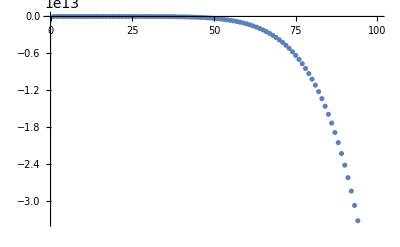

```mathematica
ListPlot[v]
```

```mathematica
(* cubic plus gaps give {-1,2} generates primes*)
```

```mathematica
Sum[If[PrimeQ[Abs[p[x]]],1,0],{x,0,99}]
```

4

```mathematica
Sum[If[PrimeQ[Abs[p[x]-1]],1,0],{x,0,99}]
```

0

```mathematica
(* test for shift*)
```

```mathematica
(* negative shifts detect primes*)
```

```mathematica
Table[Max[Union[Table[Sum[If[PrimeQ[p[x]+Prime[n]+i],1,0],{x,0,99}],{n,100}]]],{i,-100,100}]
```

{10,28,6,18,10,24,11,28,4,24,24,23,6,28,4,18,6,28,7,23,9,18,12,28,14,23,2,14,7,28,12,28,7,19,19,23,8,23,6,14,6,28,11,28,7,18,12,23,12,28,5,23,23,28,14,23,4,21,21,25,10,25,2,14,14,22,6,28,7,15,15,28,12,28,4,14,10,28,13,28,2,14,12,28,9,23,3,21,21,23,12,28,4,21,21,25,6,28,4,14,9,28,10,25,4,14,8,28,10,28,5,18,14,28,12,25,5,14,13,28,10,28,4,18,14,25,6,28,4,15,12,23,5,28,5,18,16,28,11,28,6,22,22,28,10,23,3,19,19,28,10,28,5,18,9,23,4,28,2,18,18,28,9,28,6,18,12,28,7,28,11,18,16,28,10,28,4,28,28,22,10,25,4,16,16,25,8,23,4,16,16,23,8,25,5,14,12,23,8,25,6}

```mathematica
Union[Table[Max[Union[Table[Sum[If[PrimeQ[p[x]+Prime[n]+i],1,0],{x,0,99}],{n,100}]]],{i,-100,100}]]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,18,19,21,22,23,24,25,28}

```mathematica
maxs=Max[%]
```

28

```mathematica
Union[Table[If[Max[Union[Table[Sum[If[PrimeQ[Abs[p[x]+Prime[n]+i]],1,0],{x,0,99}],{n,100}]]]==maxs,{i,Max[Union[Table[Sum[If[PrimeQ[Abs[p[x]+Prime[n]+i]],1,0],{x,0,99}],{n,100}]]]},{}],{i,-100,100}]]
```

{{},{-99,28},{-93,28},{-87,28},{-83,28},{-77,28},{-71,28},{-69,28},{-59,28},{-57,28},{-51,28},{-47,28},{-33,28},{-29,28},{-27,28},{-23,28},{-21,28},{-17,28},{-9,28},{-3,28},{1,28},{7,28},{9,28},{13,28},{19,28},{21,28},{27,28},{33,28},{37,28},{39,28},{43,28},{49,28},{51,28},{57,28},{61,28},{63,28},{67,28},{69,28},{73,28},{75,28},{77,28},{78,28}}

```mathematica
(* experiment with 100 prime gaps finds higher Prime generater*)
```

```mathematica
wp=Table[Sum[If[PrimeQ[Abs[p[x]+Prime[n]-3]],1,0],{x,0,99}],{n,-100,100}]
```

Prime::intpp: Positive integer argument expected in Prime[-100].

General::stop: Further output of Prime::intpp will be suppressed during this calculation.

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,9,10,8,10,14,12,13,14,6,5,16,11,22,19,9,4,9,12,7,10,28,16,8,12,8,17,6,12,8,15,16,10,17,8,11,14,20,21,13,6,18,13,8,6,6,9,8,14,11,7,6,6,21,10,13,6,11,9,7,16,18,11,13,11,5,11,18,7,12,15,10,11,10,21,16,10,9,2,22,7,16,12,6,15,9,10,15,11,14,6,8,11,6,15,18,9,13,5}

```mathematica
max=Max[wp]
```

28

```mathematica
q[x_]=Expand[Delete[Union[Table[If[Sum[If[PrimeQ[Abs[p[x]+Prime[n]-3]],1,0],{x,0,99}]==max,p[x]+Prime[n]-3,{}],{n,-100,100}]],2][[1]]/.x->x-1]
```

Prime::intpp: Positive integer argument expected in Prime[-100].

General::stop: Further output of Prime::intpp will be suppressed during this calculation.

4463-(103411 x)/15+(643483 x^2)/90-(19132 x^3)/5+(41617 x^4)/36-(3977 x^5)/20+(3269 x^6)/180-(41 x^7)/60

```mathematica
Reverse[CoefficientList[q[x],x]]
```

{-41/60,3269/180,-3977/20,41617/36,-19132/5,643483/90,-103411/15,4463}

```mathematica
Sum[If[PrimeQ[q[x]],1,0],{x,0,99}]
```

29

```mathematica
Sum[If[PrimeQ[q[x]],1,0],{x,0,999}]
```

149

```mathematica
x/.NSolve[q[x]==0,x]
```

{0.50788-1.07424 ⅈ,0.50788+1.07424 ⅈ,2.99818-2.49171 ⅈ,2.99818+2.49171 ⅈ,6.05374-2.04098 ⅈ,6.05374+2.04098 ⅈ,7.45764}

```mathematica
Abs[%]
```

{1.18825,1.18825,3.89843,3.89843,6.38853,6.38853,7.45764}

```mathematica
(* end*)
```

```mathematica
v=Table[If[PrimeQ[q[x]],q[x],0],{x,0,99}]
```

{4463,1867,1871,1879,1907,1931,1979,1523,-5273,-41893,0,0,0,0,0,0,-25434337,0,0,-121915193,0,0,0,0,0,0,0,-2421125569,0,0,0,0,0,0,0,-19444985801,-24267578029,0,0,-45353272493,0,0,0,0,-115163540693,0,0,-190775940181,0,0,0,0,-411129608509,-474776352341,0,-627734638589,-718869025801,0,-935576705593,0,0,-1364657824069,0,0,0,0,0,-2744957857513,0,0,0,0,-4679236994521,0,0,0,0,0,0,0,0,0,-12200420104097,0,-14560821612893,0,-17302267317109,0,0,0,0,0,0,0,0,0,0,0,0,0}

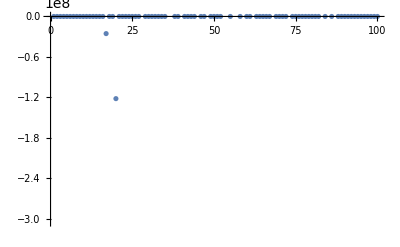

```mathematica
ListPlot[v]
```

```mathematica
wa=Table[If[PrimeQ[q[x]],1,0],{x,0,99}]
```

{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,1,0,1,1,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
min=Min[Table[If[wa[[i]]==0,i,{}],{i,Length[wa]}]]
```

11

```mathematica
Sum[wa[[i]],{i,min}]
```

10

```mathematica
Table[If[PrimeQ[q[x]],q[x],{}],{x,0,min}]
```

{4463,1867,1871,1879,1907,1931,1979,1523,-5273,-41893,{},{}}

```mathematica
Length[Union[Table[If[PrimeQ[q[x]],q[x],{}],{x,0,min-2}]]]
```

10

```mathematica
ExpandAll[FindSequenceFunction[Table[q[x],{x,0,99}],x]]
```

23707-38405 x+(250564 x^2)/9-(216523 x^3)/20+(44039 x^4)/18-(1933 x^5)/6+(413 x^6)/18-(41 x^7)/60

```mathematica
(*test output*)
```

```mathematica
(*You submitted the polynomial sequence of order 7:4463 1867 1871 1879 1907 1931 1979 1523-5273-41893
Corresponding to the equation:-41/60x7+3269/180x6-3977/20x5+41617/36x4-19132/5x3+643483/90x2-103411/15x+4463
8 primes for category 1:4463 1867 1871 1879 1907 1931 1979 1523
10 primes for category 2:4463 1867 1871 1879 1907 1931 1979 1523 5273 41893
86 primes for category 3 in the range from x=0 to 500
Score for category 1:8+1/log(10+absolute(4463*1867*1871*1879*1907*1931*1979*1523))=8.0377186971029
Score for category 2:10+1/log(10+absolute(4463*1867*1871*1879*1907*1931*1979*1523))=10.037718697103
Score for category 3:86+1/log(10+absolute(4463*1867*1871*1879*1907*1931*1979*1523))=86.037718697103
Elapsed time:0.13332486152649 seconds*)
```

```mathematica
(*end*)
```